```mathematica
SetOptions[{ParametricPlot,Plot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica",FontSize->14},PlotStyle->(Directive[AbsoluteThickness[2],#]&/@ColorData[68,"ColorList"]),ImageSize->350,Frame->True,PlotRange->All,FrameStyle->Thickness[0.001]];
```

```mathematica
rateeqs={
v1->(V1 s/K1s(1-x/(s K1))(s/K1s+x/K1x)^(n-1))/((1+(y/K1y)^n)/(1+β(y/K1y)^n)+(s/K1s+x/K1x)^n),
v2->(V2 x/K2x(1-y/(x K2)))/(1+x/K2x+y/K2y),
v3->V3 y/(K3y+y)};
parm[V1v_,V3v_,nv_]:={
s->10,
K1s->1,K1x->10^3,K1->10^3,V1->V1v,K1z->1,n->nv,K1y->1,β->10^-13,
V2->10,K2x->1,K2->10,K2y->1,
V3->V3v,K3y->1}
flux12[V1v_,yv_,nv_]:=v1/.rateeqs/.y->yv/.parm[V1v,1,nv]/.FindRoot[{
0==(v1-v2)/.rateeqs/.y->yv/.parm[V1v,1,nv]},{{x,1}}]
```

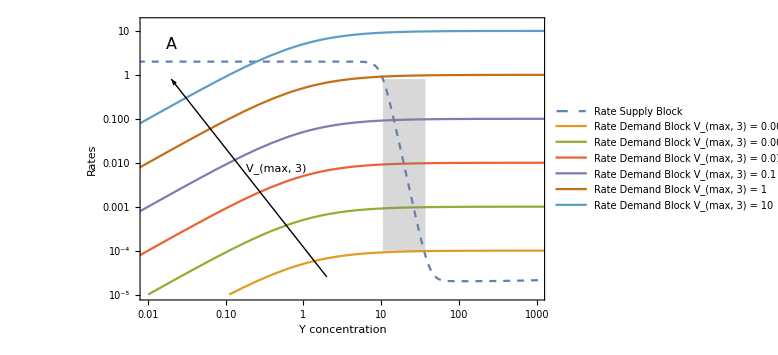

```mathematica
plA=LogLogPlot[{
flux12[2,y,8],
v3/.rateeqs/.parm[2,0.0001,8],
v3/.rateeqs/.parm[2,0.001,8],
v3/.rateeqs/.parm[2,0.01,8],
v3/.rateeqs/.parm[2,0.1,8],
v3/.rateeqs/.parm[2,1,8],
v3/.rateeqs/.parm[2,10,8]},{y,10^-5,10^4},PlotRange->{{10^-2,10^3},{10^-5,15}},FrameLabel->{"Y concentration","Rates"},PlotStyle->{Dashed,Full,Full,Full,Full,Full,Full},
Epilog->{Text[Style[A,FontSize->16],{Log[0.02],Log[5]}],Arrow[{{Log[2],Log[10^-4.6]},{Log[0.02],Log[0.8]}}],Text["V_(max, 3)",{Log[0.45],Log[0.0075]}],Gray,Opacity[0.3],Rectangle[{Log[10.5],Log[0.8]},{Log[37],Log[10^-4]}]}, PlotLegends->{"Rate Supply Block", "Rate Demand Block V_(max,  3) = 0.0001", "Rate Demand Block V_(max,  3) = 0.001", "Rate Demand Block V_(max,  3) = 0.01", "Rate Demand Block V_(max,  3) = 0.1", "Rate Demand Block V_(max,  3) = 1", "Rate Demand Block V_(max,  3) = 10"}, ImageSize->Large,FrameTicks->All]
```

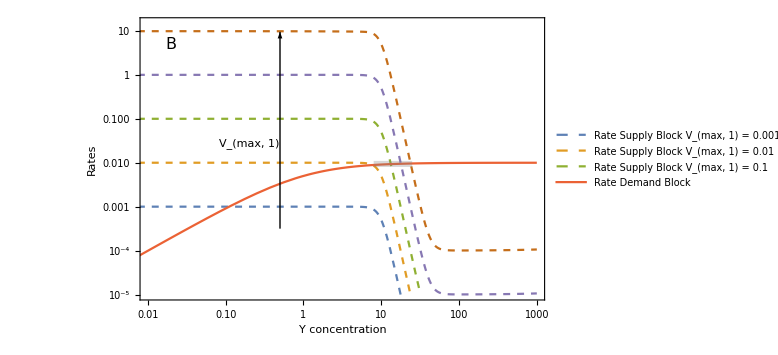

```mathematica
plB=LogLogPlot[{
flux12[0.001,y,8],
flux12[0.01,y,8],
flux12[0.1,y,8],
v3/.rateeqs/.parm[2,0.01,8],
flux12[1,y,8],
flux12[10,y,8]},{y,10^-5,10^3},PlotRange->{{10^-2,10^3},{10^-5,15}},
PlotStyle->{Dashed,Dashed,Dashed,Full,Dashed,Dashed},FrameLabel->{"Y concentration","Rates"},
Epilog->{Text[Style[B,FontSize->16],{Log[0.02],Log[5]}],Arrow[{{Log[0.5],Log[10^-3.5]},{Log[0.5],Log[9.5]}}],Text["V_(max, 1)",{Log[0.2],Log[0.0275]}],Gray,Opacity[0.3],Rectangle[{Log[8],Log[0.008]},{Log[25],Log[0.011]}]}, PlotLegends->{"Rate Supply Block V_(max,  1) = 0.001", "Rate Supply Block V_(max,  1) = 0.01", "Rate Supply Block V_(max,  1) = 0.1", "Rate Demand Block"}, ImageSize->Large,FrameTicks->All]
```

```mathematica
v1/.rateeqs
```

(s V1 (s/K1s+x/K1x)^(-1+n) (1-x/(K1 s)))/(K1s ((s/K1s+x/K1x)^n+(1+(y/K1y)^n)/(1+(y/K1y)^n β)))

```mathematica
Manipulate[
LogLinearPlot[Evaluate[v1/.rateeqs/. {
K1s->k1s,K1x->10^3,K1->k1,V1->V1v,K1z->k1z,n->nv,K1y->k1y,β->beta, x-> 0.1}/. s-> {5, 10, 20}],{y,10^-4,10^3}, PlotLegends->{"Rate V_1 with s=5", "Rate V_1 with s=10", "Rate V_1 with s=20", "Rate Supply Block V_(max,  3) = 0.1"}, ImageSize->Large, PlotRange-> {Automatic, {0, 40}}],
{{k1s,1},0.1,10},{{V1v,22},1,100},{{k1z,1},0.1,10},{{k1,10^3},10^2,10^4},{{nv,8},1,10},{{k1y,1},10^-3,10}, {{beta,10^-13},10^-14,10^-3}]
```

ReplaceAll::reps: {rateeqs} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

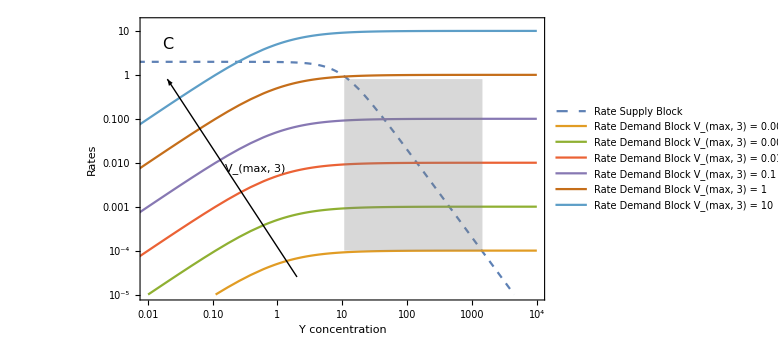

```mathematica
plC=LogLogPlot[{
flux12[2,y,2],
v3/.rateeqs/.parm[2,0.0001,2],
v3/.rateeqs/.parm[2,0.001,2],
v3/.rateeqs/.parm[2,0.01,2],
v3/.rateeqs/.parm[2,0.1,2],
v3/.rateeqs/.parm[2,1,2],
v3/.rateeqs/.parm[2,10,2]},{y,10^-5,10^4},PlotRange->{{10^-2,10^4},{10^-5,15}},FrameLabel->{"Y concentration","Rates"},
PlotStyle->{Dashed,Full,Full,Full,Full,Full,Full},
Epilog->{Text[Style[C,FontSize->16],{Log[0.02],Log[5]}],Arrow[{{Log[2],Log[10^-4.6]},{Log[0.02],Log[0.8]}}],Text["V_(max, 3)",{Log[0.45],Log[0.0075]}],Gray,Opacity[0.3],Rectangle[{Log[10.7],Log[0.8]},{Log[1450],Log[10^-4]}]},PlotLegends->{"Rate Supply Block", "Rate Demand Block V_(max,  3) = 0.0001", "Rate Demand Block V_(max,  3) = 0.001", "Rate Demand Block V_(max,  3) = 0.01", "Rate Demand Block V_(max,  3) = 0.1", "Rate Demand Block V_(max,  3) = 1", "Rate Demand Block V_(max,  3) = 10"}, ImageSize->Large,FrameTicks->All]
```

Bistability

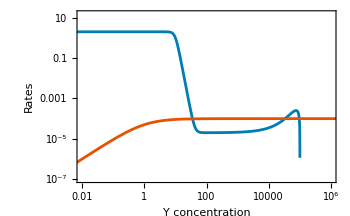

```mathematica
LogLogPlot[{
flux12[2,y,8],
v3/.rateeqs/.parm[2,0.0001,8]},{y,10^-5,10^7},PlotRange->{{10^-2,10^6},{10^-7,15}},FrameLabel->{"Y concentration","Rates"}]
```

```mathematica
parm2[V1v_,V3v_,nv_,K1yv_]:={
s->5,
K1s->1,K1x->10^3,K1->10^3,V1->V1v,K1z->1,n->nv,K1y->K1yv,β->10^-13,
V2->10,K2x->1,K2->10,K2y->1,
V3->V3v,K3y->1}
```

```mathematica
tsol[V1_,V2_,n_,K1y_]:=NDSolve[{x'[t]==v1-v2,y'[t]==v2-v3,x[0]==1,y[0]==1}/.(rateeqs/.parm2[V1,V2,n,K1y]/.{x->x[t],y->y[t]}),{x,y},{t,0,100}]
```

```mathematica
Manipulate[
Plot[Evaluate[{x[t],y[t]}/.tsol[V1,V3,n,K1y]],{t,0,100}],
{{V1,22},1,100},{{V3,3},1,100},{{n,8},1,10},{{K1y,1},10^-3,10}]
```